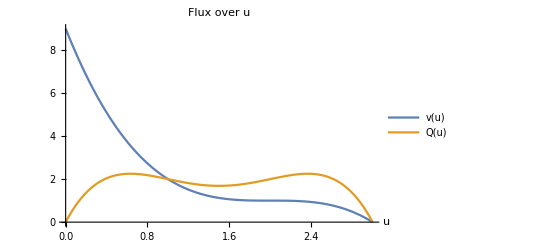

```mathematica
v[u_]=-(u-2)^3+1;
Q[u_]=u v[u];
A=Plot[{v[u],Q[u]},{u,0,3},
PlotRange->All,
PlotLegends->"Expressions",
PlotLabel->"Flux over u",
AxesLabel->Automatic]
```

```mathematica
Maximize[{Q[u],0<u&&u<1.5},u]//FullSimplify
Maximize[{Q[u],1.5<u&&u<3},u]
```

{2.25,{u→0.633975}}

{2.25,{u→2.36603}}